# Watching a Qubit: Continuous Measurement and Quantum Trajectories

A computation-first guide to continuous measurement with plain matrices and the Wolfram Language. We separate detector data, state estimates, and simulations at every step.

Mads Bahrami. Last updated August 4, 2026.

### Setting the Stage: What This Notebook Does

This notebook builds two tools. inferTrajectory updates a state estimate from a supplied detector record. simulateTrajectory generates a synthetic record and a matching state path from a model and random noise.

Computation has three roles here: infer a state from data, illustrate a model with simulation, and check code against a separate calculation.

Keep these distinctions fixed:

Object | Source | Status
Detector current from an experiment | Detector electronics | Observed data
State path computed from an experimental record | Record, model, and initial state | Inferred, not directly observed
Synthetic current and state path | Model and random numbers | Simulated, useful for insight but not experimental evidence
Average of simulations compared with a master-equation solver | Two calculations of the same model | Numerical code check, not an experimental test

Evaluate the cells from top to bottom. The code uses only built-in Wolfram Language functions. We set ℏ=1, so Hamiltonians have units of inverse time.

## Part I: The Equation and the Detector Record

When environmental effects have no relevant memory, the state ρ obeys the Lindblad master equation

dρ/dt=-i[H,ρ]+∑_k 𝒟[c_k]ρ,    𝒟[c]ρ=cρ c^†-1/2{c^†c,ρ}.

This equation gives the state averaged over all possible detector records when no record is used. It has no random term.

Now monitor some channels L_r with efficiencies 0≤η_r≤1. Leave the other channels V_j unmonitored. The state estimate based on the detector record obeys

d ρ_c=-i[H,ρ_c]dt+∑_j 𝒟[V_j]ρ_c dt+∑_r 𝒟[L_r]ρ_c dt+∑_r √η_r ℋ[L_r]ρ_c d W_r,

where

ℋ[c]ρ=cρ+ρ c^†-Tr[(c+c^†)ρ]ρ.

The detector supplies a real readout increment

d R_r=√η_r Tr[(L_r+L_r^†)ρ_c]dt+d W_r.

Each d W_r is a zero-mean Gaussian increment with variance dt. The measured current over one discrete step is I_r=d R_r/dt.

The equation updates a state estimate after each detector reading. That estimate depends on the record, the model, and the initial state. It is not another detector output.

Rates are included in the operators. A channel with rate γ and dimensionless operator A is passed as √γ A.

Two limits provide checks. If every η_r=0, the record carries no state information and the state follows the master equation. In the continuous-time equation, a pure record-based state remains pure when every loss or noise channel is monitored at unit efficiency. The mean over many simulated records returns the master-equation state in the same limit. A finite-step calculation also has time-step error.

## Part II: A State Update That Preserves Positivity

A direct Euler step can produce a negative eigenvalue. We instead use the update of Rouchon and Ralph (arXiv:1410.5345):

ρ_(n+1)=((ρ̃)_(n+1))/(Tr(ρ̃)_(n+1)),

(ρ̃)_(n+1)=M ρ_n M^†+dt∑_j V_j ρ_n V_j^†+dt∑_r (1-η_r)L_r ρ_n L_r^†,

M=1-(iH+1/2∑_r L_r^†L_r+1/2∑_j V_j^†V_j)dt+∑_r √η_r L_r d R_r+1/2∑_(r,s) √(η_r η_s)L_r L_s(d R_r d R_s-δ_rs dt).

Every term in (ρ̃)_(n+1) has the form Aρ A^† with a nonnegative coefficient. Therefore a valid input state stays positive when dt≥0, 0≤η_r≤1, and the normalization is nonzero.

This is a statement about physical validity, not numerical accuracy. A large step can still give a poor approximation to the continuous equation. We must check convergence as dt decreases.

The double sum can be computed without building all operator pairs. Define

S=∑_r √η_r L_r d R_r.

Then

1/2∑_(r,s) √(η_r η_s)L_r L_s(d R_r d R_s-δ_rs dt)=1/2 S^2-dt/2∑_r η_r L_r^2.

This is an exact algebraic identity. The order L_r L_s is unchanged.

First define input checks and prepare the fixed parts of the model:

```mathematica
ClearAll[realNumberQ, numericSquareMatrixQ, hermitianMatrixQ,
  densityMatrixQ, prepareModel];

realNumberQ[x_] := NumericQ[x] && TrueQ[Im@N[x] == 0];

numericSquareMatrixQ[m_] := MatrixQ[m, NumericQ] &&
  With[{dims = Dimensions[m]},
   Length[dims] == 2 && First[dims] == Last[dims] && First[dims] > 0];

hermitianMatrixQ[m_, tolerance_ : 10^-10] :=
  numericSquareMatrixQ[m] &&
   Max[Abs[N[m] - ConjugateTranspose[N[m]]]] <= tolerance;

densityMatrixQ[m_, tolerance_ : 10^-10] :=
  hermitianMatrixQ[m, tolerance] &&
   Abs[Tr[N[m]] - 1] <= tolerance &&
   Min[Eigenvalues[(N[m] + ConjugateTranspose[N[m]])/2]] >= -tolerance;

prepareModel[initialState_, hamiltonian_, measuredOperators_, efficiencies_,
   unmonitoredOperators_] := Module[
  {state = N[initialState], ham = N[hamiltonian],
   measured = N[measuredOperators], unmonitored = N[unmonitoredOperators],
   eta, dimension, operators},

  If[!densityMatrixQ[state],
   Return@Failure["InvalidInitialState",
     <|"MessageTemplate" -> "The initial state must be a positive, unit-trace density matrix."|>]];

  dimension = Length[state];
  If[!ListQ[measured] || !ListQ[unmonitored] ||
    (efficiencies =!= Automatic && !ListQ[efficiencies]),
   Return@Failure["InvalidOptions",
     <|"MessageTemplate" -> "Measured operators, efficiencies, and unmonitored operators must be lists."|>]];
  eta = N@If[efficiencies === Automatic,
     ConstantArray[1, Length[measured]], efficiencies];
  If[!AllTrue[Join[measured, unmonitored], numericSquareMatrixQ],
   Return@Failure["InvalidChannel",
     <|"MessageTemplate" -> "Every channel operator must be a numerical square matrix."|>]];
  operators = Join[{ham}, measured, unmonitored];

  If[!hermitianMatrixQ[ham],
   Return@Failure["InvalidHamiltonian",
     <|"MessageTemplate" -> "The Hamiltonian must be a numerical Hermitian matrix."|>]];
  If[!AllTrue[operators, Dimensions[#] == {dimension, dimension} &],
   Return@Failure["DimensionMismatch",
     <|"MessageTemplate" -> "The state, Hamiltonian, and all channel operators must have the same dimension."|>]];
  If[Length[eta] != Length[measured] ||
    !VectorQ[eta, realNumberQ] || !AllTrue[eta, 0 <= # <= 1 &],
   Return@Failure["InvalidEfficiency",
     <|"MessageTemplate" -> "Provide one real efficiency between 0 and 1 for each measured channel."|>]];

  <|"InitialState" -> state, "Hamiltonian" -> ham,
   "MeasuredOperators" -> measured, "Efficiencies" -> eta,
   "UnmonitoredOperators" -> unmonitored,
   "Identity" -> IdentityMatrix[dimension],
   "DriftRate" -> I ham +
     Total[ConjugateTranspose[#] . # & /@ Join[measured, unmonitored]]/2,
   "CorrectionRate" ->
     Total[MapThread[#1 (#2 . #2) &, {eta, measured}]]/2|>
  ];
```

Now build one state step from the fixed model. The input stepData is {stepSize, readoutIncrements}:

```mathematica
ClearAll[makeStateStep, trajectoryFailureTag];

makeStateStep[model_Association] := With[
  {identity = model["Identity"], driftRate = model["DriftRate"],
   correctionRate = model["CorrectionRate"],
   measured = model["MeasuredOperators"], eta = model["Efficiencies"],
   unmonitored = model["UnmonitoredOperators"]},
  Function[{state, stepData},
   Module[{stepSize = First[stepData], readout = Last[stepData],
     signalStep, measurementMatrix, numerator, normalization},
    signalStep = Total@Join[{0 identity},
      MapThread[#1 Sqrt[#2] #3 &, {readout, eta, measured}]];
    measurementMatrix = identity - stepSize driftRate + signalStep +
      signalStep . signalStep/2 - stepSize correctionRate;
    numerator = measurementMatrix . state .
       ConjugateTranspose[measurementMatrix] +
      stepSize Total[# . state . ConjugateTranspose[#] & /@ unmonitored] +
      stepSize Total[
        MapThread[(1 - #2) (#1 . state . ConjugateTranspose[#1]) &,
         {measured, eta}]];
    normalization = Re@Tr[numerator];
    If[!TrueQ[normalization > 10^-14],
     Throw[Failure["ZeroNormalization",
       <|"MessageTemplate" -> "This step has zero numerical weight. Reduce the step size or check the record."|>],
      trajectoryFailureTag]];
    numerator/normalization
    ]]
  ];
```

The next function uses supplied readout increments. This is the function to use with calibrated experimental data:

```mathematica
ClearAll[inferTrajectory, currentFromIncrements];

Options[inferTrajectory] = {"Efficiencies" -> Automatic,
   "UnmonitoredOperators" -> {}};

currentFromIncrements[increments_, stepSizes_] :=
  MapThread[#1/#2 &, {increments, stepSizes}];

inferTrajectory[initialState_, hamiltonian_,
   measuredOperators_, recordIncrements_, stepSizes_,
   OptionsPattern[]] := Module[{model, steps = N[stepSizes], records = N[recordIncrements],
   stateStep, states, times, channelCount},

  model = prepareModel[initialState, hamiltonian, measuredOperators,
    OptionValue["Efficiencies"], OptionValue["UnmonitoredOperators"]];
  If[FailureQ[model], Return[model]];
  channelCount = Length[model["MeasuredOperators"]];

  If[!ListQ[records] || !ListQ[steps] || Length[records] != Length[steps] ||
    !AllTrue[steps, realNumberQ[#] && # > 0 &] ||
    !AllTrue[records, VectorQ[#, realNumberQ] && Length[#] == channelCount &],
   Return@Failure["InvalidRecord",
     <|"MessageTemplate" -> "Use one positive step size and one readout vector per time step."|>]];

  stateStep = makeStateStep[model];
  states = Catch[
    FoldList[stateStep, model["InitialState"], Transpose[{steps, records}]],
    trajectoryFailureTag];
  If[FailureQ[states], Return[states]];
  times = Accumulate@Join[{0.}, steps];

  <|"Times" -> times, "States" -> states,
   "RecordIncrements" -> records,
   "Current" -> currentFromIncrements[records, steps]|>
  ];
```

The simulator draws Gaussian noise and generates a synthetic record. It also returns the state path used to generate that record:

```mathematica
ClearAll[makeStepSizes, readoutIncrement, simulateTrajectory];

Options[simulateTrajectory] = Options[inferTrajectory];

makeStepSizes[dt_, finalTime_] := Module[
  {step = N[dt], stop = N[finalTime], count, remainder, tolerance},
  If[!realNumberQ[step] || !realNumberQ[stop] || step <= 0 || stop < 0,
   Return@Failure["InvalidTime",
     <|"MessageTemplate" -> "The step size must be positive and the final time must be nonnegative."|>]];
  tolerance = 100 $MachineEpsilon Max[1., step, stop];
  count = Floor[stop/step];
  remainder = stop - count step;
  If[count > 0 && remainder < tolerance, remainder = 0.];
  If[step - remainder < tolerance, count += 1; remainder = 0.];
  Join[ConstantArray[step, count], If[remainder > 0, {remainder}, {}]]
  ];

readoutIncrement[state_, measuredOperators_, efficiencies_, stepSize_, noise_] :=
  MapThread[
   Sqrt[#3] Re@Tr[(#1 + ConjugateTranspose[#1]) . state] stepSize + #2 &,
   {measuredOperators, noise, efficiencies}];

simulateTrajectory[initialState_, hamiltonian_,
   measuredOperators_, dt_, finalTime_,
   OptionsPattern[]] := Module[
  {model, steps, noise, stateStep, simulationStep, states, recordBag, records, times},

  model = prepareModel[initialState, hamiltonian, measuredOperators,
    OptionValue["Efficiencies"], OptionValue["UnmonitoredOperators"]];
  If[FailureQ[model], Return[model]];
  steps = makeStepSizes[dt, finalTime];
  If[FailureQ[steps], Return[steps]];

  noise = RandomVariate[NormalDistribution[0, Sqrt[#]],
      Length[model["MeasuredOperators"]]] & /@ steps;
  stateStep = makeStateStep[model];
  simulationStep = Function[{state, stepData},
    Module[{stepSize = First[stepData], noiseVector = Last[stepData], readout},
     readout = readoutIncrement[state, model["MeasuredOperators"],
       model["Efficiencies"], stepSize, noiseVector];
     Sow[readout, "record"];
     stateStep[state, {stepSize, readout}]
     ]];

  {states, recordBag} = Reap[
    Catch[FoldList[simulationStep, model["InitialState"],
      Transpose[{steps, noise}]], trajectoryFailureTag], "record"];
  If[FailureQ[states], Return[states]];
  records = If[recordBag === {}, {}, First[recordBag]];
  times = Accumulate@Join[{0.}, steps];

  <|"Times" -> times, "States" -> states,
   "RecordIncrements" -> records,
   "Current" -> currentFromIncrements[records, steps]|>
  ];
```

inferTrajectory contains no random-number generator. Its state path is inferred from its input record. simulateTrajectory does use random numbers. Its outputs are synthetic.

Define the qubit matrices:

```mathematica
ClearAll[X, Y, Z, identity2, jMinus, densityMatrix, blochVector, purity];
X = PauliMatrix[1]; Y = PauliMatrix[2]; Z = PauliMatrix[3];
identity2 = IdentityMatrix[2];
jMinus = (X - I Y)/2;
densityMatrix[stateVector_] := Outer[Times, stateVector, Conjugate[stateVector]];
blochVector[state_] := Re[Tr[state . #] & /@ {X, Y, Z}];
purity[state_] := Re@Tr[state . state];
```

blochVector[state] returns the three averages of X, Y, and Z. purity[state] returns Tr(ρ^2); it equals one for a pure state. When the state is inferred, both quantities are inferred too. They are not detector readings.

With our basis convention,

J_-=(0 | 0
1 | 0).

It sends 0 to 1. Thus 0 is the excited state and 1 is the ground state in this notebook.

Define three pure states:

```mathematica
ket0 = {1, 0}; ket1 = {0, 1}; ketPlus = {1, 1}/Sqrt[2];
```

Only a pure-state density matrix has the form ψψ. A general density matrix can be mixed.

Check the lowering operator and the north-pole Bloch vector:

```mathematica
{MatrixForm[jMinus], jMinus . ket0, jMinus . ket1,
 blochVector[densityMatrix[ket0]]}
```

{(0 | 0
1 | 0),{0,1},{0,0},{0,0,1}}

Check one rejected input:

```mathematica
simulateTrajectory[densityMatrix[ket0], 0. identity2, {jMinus}, 0.01, 0.1,
 "Efficiencies" -> {1.2}]
```

Failure[…]

The call returns a Failure before any random path is generated. An efficiency above one is not physical.

Check two boundary cases together: no recorded channel and a final step shorter than dt:

```mathematica
boundaryExample = simulateTrajectory[densityMatrix[ket0], 0. identity2, {},
  0.007, 0.023, "UnmonitoredOperators" -> {Sqrt[0.2] jMinus}];

<|"step sizes" -> Differences[boundaryExample["Times"]],
 "record dimensions" -> Dimensions[boundaryExample["RecordIncrements"]],
 "state dimensions" -> Dimensions[boundaryExample["States"]],
 "ends at requested time" ->
   Chop[Last[boundaryExample["Times"]] - 0.023] == 0|>
```

<|step sizes→{0.007,0.007,0.007,0.002},record dimensions→{4,0},state dimensions→{5,2,2},ends at requested time→True|>

The result has four state updates, no recorded values, and a last step of 0.002. The unmonitored channel still changes the state.

## Part III: One Synthetic Path and the Mean over Many Paths

Use a driven qubit whose Z component is monitored. This section checks code. It does not analyze experimental data.

```mathematica
omega = 1.0; gamma = 0.4;
hamiltonian = omega X;
measuredOperators = {Sqrt[gamma] Z};
initialState = densityMatrix[ket0];
dt = 0.005; finalTime = 10.0;
```

Define an independent solver for the master equation:

```mathematica
ClearAll[dissipator, masterEquationSolution];

dissipator[channel_, state_] :=
  channel . state . ConjugateTranspose[channel] -
   (ConjugateTranspose[channel] . channel . state +
      state . ConjugateTranspose[channel] . channel)/2;

masterEquationSolution[initialState_, hamiltonian_, channels_,
   {time_, start_, stop_}] := Module[{state},
  NDSolveValue[{
    state'[time] == -I (hamiltonian . state[time] - state[time] . hamiltonian) +
      Total[dissipator[#, state[time]] & /@ channels],
    state[start] == initialState}, state, {time, start, stop}]
  ];
```

Generate one synthetic record and state path:

```mathematica
oneSimulation = BlockRandom[SeedRandom[1];
  simulateTrajectory[initialState, hamiltonian, measuredOperators, dt, finalTime]];
```

Check unit trace, equality to the conjugate transpose, and positivity along this path:

```mathematica
oneStates = oneSimulation["States"];
<|"largest trace error" -> Max[Abs[Tr[#] - 1] & /@ oneStates],
 "largest Hermiticity error" ->
   Max[Max[Abs[# - ConjugateTranspose[#]]] & /@ oneStates],
 "smallest eigenvalue" ->
   Min[Flatten[Eigenvalues[(# + ConjugateTranspose[#])/2] & /@ oneStates]]|>
```

<|largest trace error→2.22045×10^-16,largest Hermiticity error→1.4988×10^-15,smallest eigenvalue→-5.92756×10^-16|>

The errors should be at numerical roundoff. Positivity is preserved, but accuracy still depends on dt.

Feed the synthetic record into the separate inference function:

```mathematica
reconstructed = inferTrajectory[initialState, hamiltonian, measuredOperators,
  oneSimulation["RecordIncrements"], Differences[oneSimulation["Times"]]];
Max[Norm[#1 - #2, "Frobenius"] & @@@
  Transpose[{oneSimulation["States"], reconstructed["States"]}]]
```

3.67604×10^-13

The two state paths agree because they use the same record and the same update rule. This checks the separation between simulation and inference. It is not an experimental validation.

Compare one state estimate from a synthetic record with the smooth master-equation result:

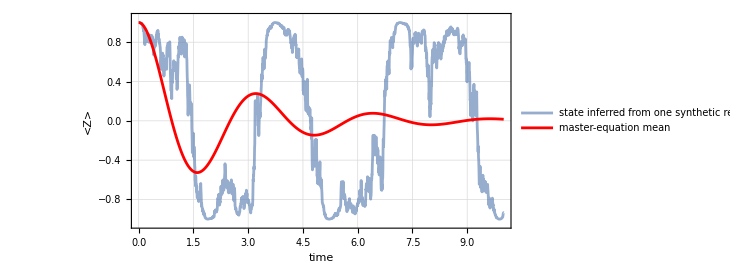

```mathematica
timeGrid = oneSimulation["Times"];
masterSolution = masterEquationSolution[initialState, hamiltonian,
  measuredOperators, {time, 0, finalTime}];
masterStates = masterSolution /@ timeGrid;

ListLinePlot[{
  Transpose[{timeGrid, blochVector[#][[3]] & /@ oneStates}],
  Transpose[{timeGrid, blochVector[#][[3]] & /@ masterStates}]},
 PlotStyle -> {Directive[Opacity[0.65], ColorData[97, 1]], Directive[Thick, Red]},
 PlotLegends -> {"state inferred from one synthetic record", "master-equation mean"},
 Frame -> True, FrameLabel -> {"time", "<Z>"}, GridLines -> Automatic,
 PlotRange -> {-1.05, 1.05}, ImageSize -> 540, AspectRatio -> 1/2]
```

Check time-step convergence without random scatter by setting the efficiency to zero. The channel still acts, but every run gives the same state:

```mathematica
timeStepValues = {0.08, 0.04, 0.02, 0.01};
timeStepErrors = AssociationThread[timeStepValues,
  Norm[Last[simulateTrajectory[initialState, hamiltonian, measuredOperators, #,
        finalTime, "Efficiencies" -> {0.0}]["States"]] -
      masterSolution[finalTime], "Frobenius"] & /@ timeStepValues]
```

<|0.08→0.00329952,0.04→0.00179629,0.02→0.000936293,0.01→0.000477894|>

The error decreases as the step is halved. Positivity alone would not show this accuracy check.

Now average 150 independent simulations:

```mathematica
simulationCount = 150;
simulatedStateSets = BlockRandom[SeedRandom[42];
  Table[simulateTrajectory[initialState, hamiltonian, measuredOperators, dt,
     finalTime]["States"], {simulationCount}]];
meanStates = Mean[simulatedStateSets];
```

Compare the full mean density matrix with the master-equation solution at every time:

```mathematica
Max[Norm[#1 - #2, "Frobenius"] & @@@ Transpose[{meanStates, masterStates}]]
```

0.0803428

Plot one component:

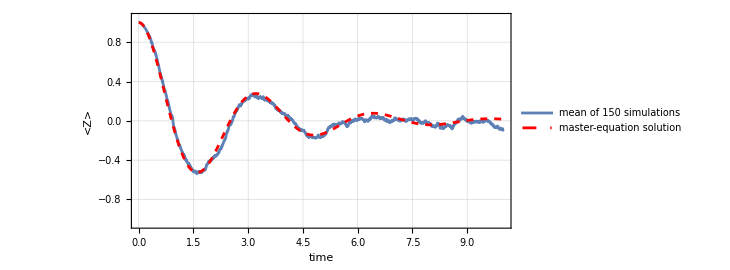

```mathematica
ListLinePlot[{
  Transpose[{timeGrid, blochVector[#][[3]] & /@ meanStates}],
  Transpose[{timeGrid, blochVector[#][[3]] & /@ masterStates}]},
 PlotStyle -> {Directive[Thick, ColorData[97, 1]], Directive[Dashed, Red]},
 PlotLegends -> {"mean of 150 simulations", "master-equation solution"},
 Frame -> True, FrameLabel -> {"time", "<Z>"}, GridLines -> Automatic,
 PlotRange -> {-1.05, 1.05}, ImageSize -> 540, AspectRatio -> 1/2]
```

Small differences remain because only 150 paths were used. Agreement checks that the random update has the correct mean. Both curves come from the same model, so this is a code check, not a measurement.

## Part IV: Strong and Weak Monitoring

For H=ΩX and a monitored operator √γ Z, the value z=⟨Z⟩ averaged over all possible records satisfies

z^(..)+2γ ż+4 Ω^2 z=0,    z(0)=1,    ż(0)=0.

The two exponents are

-γ±√(γ^2-4 Ω^2).

Strong monitoring means γ≫Ω. The slow rate is then

γ-√(γ^2-4 Ω^2)≃(2 Ω^2)/γ.

Thus stronger monitoring slows the change of Z. This slowing is called the quantum Zeno effect.

Define the exact solution for the two noncritical cases:

```mathematica
ClearAll[zDephasing];
zDephasing[t_, omega_, gamma_] := With[{q = gamma^2 - 4 omega^2},
  Which[
   q > 0, Exp[-gamma t] (Cosh[Sqrt[q] t] + gamma Sinh[Sqrt[q] t]/Sqrt[q]),
   q < 0, Exp[-gamma t] (Cos[Sqrt[-q] t] + gamma Sin[Sqrt[-q] t]/Sqrt[-q]),
   True, Exp[-gamma t] (1 + gamma t)]];
```

Check the equation, initial values, and strong-monitoring rate without choosing numerical values:

```mathematica
ClearAll[symbolicTime, symbolicOmega, symbolicGamma, symbolicZ];

symbolicZ = Exp[-symbolicGamma symbolicTime] (
   Cosh[Sqrt[symbolicGamma^2 - 4 symbolicOmega^2] symbolicTime] +
    symbolicGamma Sinh[Sqrt[symbolicGamma^2 - 4 symbolicOmega^2] symbolicTime]/
     Sqrt[symbolicGamma^2 - 4 symbolicOmega^2]);

FullSimplify[{
  D[symbolicZ, {symbolicTime, 2}] +
   2 symbolicGamma D[symbolicZ, symbolicTime] +
   4 symbolicOmega^2 symbolicZ,
  symbolicZ /. symbolicTime -> 0,
  D[symbolicZ, symbolicTime] /. symbolicTime -> 0,
  Limit[symbolicGamma (symbolicGamma -
      Sqrt[symbolicGamma^2 - 4 symbolicOmega^2]),
    symbolicGamma -> Infinity]},
 Assumptions -> symbolicGamma > 2 symbolicOmega > 0]
```

{0,1,0,2 symbolicOmega^2}

The result is {0, 1, 0, 2 symbolicOmega^2}. It verifies the equation, both initial values, and the coefficient in the slow rate.

Choose rates that are clearly separated:

```mathematica
omegaD = 1.0; gammaStrong = 20.0; gammaWeak = 0.1;
dtD = 0.0025; finalTimeD = 8.0;
timeGridD = Range[0., finalTimeD, dtD];
```

Plot the exact mean curves:

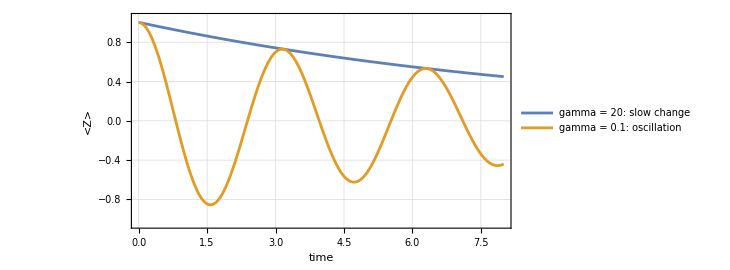

```mathematica
ListLinePlot[{
  Transpose[{timeGridD, zDephasing[timeGridD, omegaD, gammaStrong]}],
  Transpose[{timeGridD, zDephasing[timeGridD, omegaD, gammaWeak]}]},
 PlotStyle -> {Directive[Thick, ColorData[97, 1]], Directive[Thick, ColorData[97, 2]]},
 PlotLegends -> {"gamma = 20: slow change", "gamma = 0.1: oscillation"},
 Frame -> True, FrameLabel -> {"time", "<Z>"}, GridLines -> Automatic,
 PlotRange -> {-1.05, 1.05}, ImageSize -> 540, AspectRatio -> 1/2]
```

Check the master-equation solver against the exact result:

```mathematica
strongMaster = masterEquationSolution[densityMatrix[ket0], omegaD X,
  {Sqrt[gammaStrong] Z}, {time, 0, finalTimeD}];
weakMaster = masterEquationSolution[densityMatrix[ket0], omegaD X,
  {Sqrt[gammaWeak] Z}, {time, 0, finalTimeD}];

<|"strong-rate error" ->
   Max[Abs[(blochVector[strongMaster[#]][[3]] & /@ timeGridD) -
      zDephasing[timeGridD, omegaD, gammaStrong]]],
 "weak-rate error" ->
   Max[Abs[(blochVector[weakMaster[#]][[3]] & /@ timeGridD) -
      zDephasing[timeGridD, omegaD, gammaWeak]]]|>
```

<|strong-rate error→6.68819×10^-8,weak-rate error→1.93017×10^-6|>

One synthetic path in each regime gives intuition about individual records:

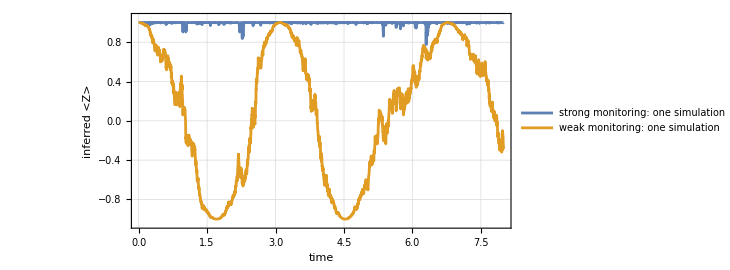

```mathematica
strongSimulation = BlockRandom[SeedRandom[7];
  simulateTrajectory[densityMatrix[ket0], omegaD X,
    {Sqrt[gammaStrong] Z}, dtD, finalTimeD]];
weakSimulation = BlockRandom[SeedRandom[7];
  simulateTrajectory[densityMatrix[ket0], omegaD X,
    {Sqrt[gammaWeak] Z}, dtD, finalTimeD]];

ListLinePlot[{
  Transpose[{strongSimulation["Times"],
    blochVector[#][[3]] & /@ strongSimulation["States"]}],
  Transpose[{weakSimulation["Times"],
    blochVector[#][[3]] & /@ weakSimulation["States"]}]},
 PlotStyle -> {ColorData[97, 1], ColorData[97, 2]},
 PlotLegends -> {"strong monitoring: one simulation", "weak monitoring: one simulation"},
 Frame -> True, FrameLabel -> {"time", "inferred <Z>"}, GridLines -> Automatic,
 PlotRange -> {-1.05, 1.05}, ImageSize -> 540, AspectRatio -> 1/2]
```

The strong case stays near a Z eigenstate for long intervals. The weak case follows the drive more freely. These paths illustrate the model. Only a detector record from an experiment could support a claim about a real device.

## Part V: Monitored Spontaneous Emission

Now monitor emission through J_-. In homodyne detection, the instrument records one real component of the emitted field. With a complete unit-efficiency record and a pure initial state, the inferred state remains pure.

```mathematica
omegaS = 2.0; detuningS = 1.0;
hamiltonianS = (omegaS X + detuningS Z)/2;
gammaS = 0.2; measuredS = {Sqrt[gammaS] jMinus};
initialStateS = densityMatrix[ketPlus];
dtS = 0.01; finalTimeS = 10.0;
```

Generate five synthetic paths:

```mathematica
emissionSimulations = BlockRandom[SeedRandom[3];
  Table[simulateTrajectory[initialStateS, hamiltonianS, measuredS, dtS,
    finalTimeS], {5}]];
emissionBlochPaths = (blochVector /@ #["States"]) & /@ emissionSimulations;
```

Draw a simple Bloch sphere and overlay the paths:

```mathematica
blochSphere = Graphics3D[{
    {Opacity[0.12], LightBlue, Sphere[]},
    {Gray, Line[{{-1.1, 0, 0}, {1.1, 0, 0}}],
     Line[{{0, -1.1, 0}, {0, 1.1, 0}}],
     Line[{{0, 0, -1.1}, {0, 0, 1.1}}]}},
   Boxed -> False, PlotRange -> 1.15, ImageSize -> 420];

Show[blochSphere,
 Graphics3D[{Thick,
   MapIndexed[{ColorData[97, First@#2], Line@#1} &, emissionBlochPaths]}]]
```

-Graphics3D-

Each curve is a possible inferred state path for a possible synthetic record. The plot shows model behavior, not observed motion.

Check the mean of many simulations against the master equation:

```mathematica
emissionTimeGrid = emissionSimulations[[1]]["Times"];
emissionMaster = masterEquationSolution[initialStateS, hamiltonianS, measuredS,
  {time, 0, finalTimeS}];
emissionMasterStates = emissionMaster /@ emissionTimeGrid;
emissionStateSets = BlockRandom[SeedRandom[11];
  Table[simulateTrajectory[initialStateS, hamiltonianS, measuredS, dtS,
    finalTimeS]["States"], {150}]];
emissionMeanStates = Mean[emissionStateSets];

Max[Norm[#1 - #2, "Frobenius"] & @@@
  Transpose[{emissionMeanStates, emissionMasterStates}]]
```

0.0888247

This extends the numerical mean-state check from Z monitoring to emission. It still tests the implementation, not a laboratory system.

## Part VI: What a Detector Record Can Show

An experimental detector directly supplies a current. From that record we can compute its mean, how readings separated in time vary together, and how power is spread across frequency. The standard names for the last two quantities are autocovariance and power spectrum.

The record below is synthetic. The analysis is the same analysis one can apply to calibrated experimental data, but its result is only a prediction of the chosen model.

```mathematica
omegaC = 3.5; gammaC = 0.7;
hamiltonianC = omegaC Y/2;
measuredC = {Sqrt[gammaC] jMinus};
dtC = 0.01; finalTimeC = 1200.0;

longSimulation = BlockRandom[SeedRandom[1];
  simulateTrajectory[densityMatrix[ket0], hamiltonianC, measuredC, dtC,
    finalTimeC]];
simulatedCurrent = Re@longSimulation["Current"][[All, 1]];
```

Check the current's sample mean and standard deviation:

```mathematica
{Length[simulatedCurrent], Mean[simulatedCurrent],
 StandardDeviation[simulatedCurrent], 1/Sqrt[dtC]}
```

{120000,-0.156682,10.003,10.}

The white-noise part of the current has standard deviation 1/√dt. A single sample is therefore noisy. Correlations across time can reveal repeated motion.

The autocovariance measures how readings separated by a chosen delay vary together. Compute it with a fast Fourier transform. Each delay is divided by its own number of data pairs:

```mathematica
ClearAll[autocovariance];

autocovariance[data_, maximumLag_Integer, dt_, stride_Integer : 1] := Module[
  {centered, count = Length[data], paddedLength,
   sums, lags},
  If[!VectorQ[data, realNumberQ] || Length[data] < 2 || maximumLag < 0 ||
    !realNumberQ[dt] || dt <= 0 || stride <= 0,
   Return@Failure["InvalidData",
     <|"MessageTemplate" -> "Use a numerical record, a nonnegative maximum lag, a positive step, and a positive stride."|>]];
  centered = N[data - Mean[data]];
  lags = Range[0, Min[maximumLag, count - 1], stride];
  paddedLength = 2^Ceiling[Log[2, 2 count - 1]];
  sums = Re@InverseFourier[
     Abs[Fourier[PadRight[centered, paddedLength],
        FourierParameters -> {1, -1}]]^2,
     FourierParameters -> {1, -1}];
  Transpose[{dt lags, sums[[lags + 1]]/(count - lags)}]
  ];
```

Skip the zero-lag point in the plot because it contains the large white-noise variance:

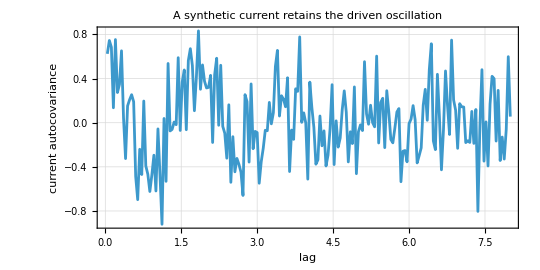

```mathematica
currentCovariance = Rest@autocovariance[simulatedCurrent, Floor[8/dtC], dtC, 4];

ListLinePlot[currentCovariance, Frame -> True, ImageSize -> 540,
 AspectRatio -> 1/2, GridLines -> Automatic, PlotRange -> All,
 FrameLabel -> {"lag", "current autocovariance"},
 PlotLabel -> "A synthetic current retains the driven oscillation"]
```

For ideal white noise, the expected covariance is zero at every nonzero lag. A finite record still has random scatter there. The same noise also changes the future state, so it is incorrect to say that shot noise contributes nothing away from zero lag.

The power spectrum shows signal strength against frequency. To reduce random scatter, divide the record into separate segments, subtract each segment's mean, and average the resulting estimates:

```mathematica
ClearAll[averagedPeriodogram];

averagedPeriodogram[data_, dt_, segmentLength_Integer] := Module[
  {segments, twoSided, meanSpectrum, indices, frequencies},
  If[!VectorQ[data, realNumberQ] || !realNumberQ[dt] || dt <= 0 ||
    segmentLength < 3 || segmentLength > Length[data],
   Return@Failure["InvalidData",
     <|"MessageTemplate" -> "Use a numerical record, a positive step, and a segment length between 3 and the record length."|>]];
  segments = Partition[N[data], segmentLength, segmentLength];
  twoSided = (dt/segmentLength) Abs[
        Fourier[# - Mean[#], FourierParameters -> {1, -1}]]^2 & /@ segments;
  meanSpectrum = Mean[twoSided];
  indices = Range[2, Ceiling[segmentLength/2]];
  frequencies = 2 Pi Range[1, Length[indices]]/(segmentLength dt);
  Transpose[{frequencies, 2 meanSpectrum[[indices]]}]
  ];
```

Compute the spectrum of the current, not the increments. Under this one-sided convention, ideal unit white noise has a flat level of 2:

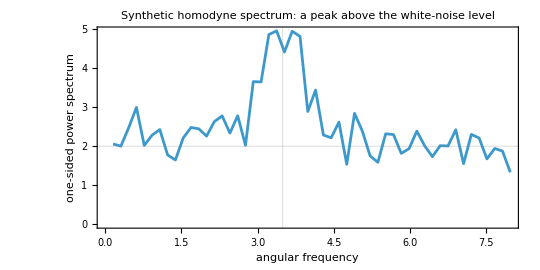

```mathematica
spectrum = Select[averagedPeriodogram[simulatedCurrent, dtC, 4096],
   First[#] <= 8 &];
oscillationFrequency = Sqrt[omegaC^2 - gammaC^2/16];

ListLinePlot[spectrum, Frame -> True, ImageSize -> 540, AspectRatio -> 1/2,
 PlotRange -> All, GridLines -> {{oscillationFrequency}, {2}},
 FrameLabel -> {"angular frequency", "one-sided power spectrum"},
 PlotLabel -> "Synthetic homodyne spectrum: a peak above the white-noise level"]
```

Read the largest peak in the driven band:

```mathematica
MaximalBy[Select[spectrum, 2 <= First[#] <= 5 &], Last][[1]]
```

{3.37476,4.95093}

For this driven, emitting qubit, the equations for the mean Bloch vector oscillate at

ω_osc=√(Ω_C^2-γ_C^2/16)

and decay at rate 3 γ_C/4. The spectrum should show a peak near ω_osc. Its detailed shape depends on the full model. A decay rate must be obtained from a fit with stated assumptions; it is not simply the width read by eye.

### What Is Observable, and What Is a Test?

Given an experimental current, its mean, autocovariance, and spectrum are calculated directly from observed data. A spectral peak is therefore an observed feature of that record. Identifying the peak with a system parameter still requires a model.

A state path is different. It is inferred by applying inferTrajectory to the record. Its Bloch vector, purity, and expectation values are properties of the estimate, not raw detector readings.

Using the same record both to construct the state estimate and to compare its mean signal with that record is a consistency check, not an independent test. Stronger tests use data that were not used in the inference: a later measurement, a separate detector channel, repeated final-state measurements, or a prediction made before more data arrive.

Experiments have used continuous records to estimate mechanical quantum states in real time and have tested those estimates with later or separate measurements: Magrini et al., Nature 595, 373-377 (2021) and Rossi et al., Physical Review Letters 123, 163601 (2019). Those results support the method in those systems. A synthetic trajectory in this notebook does not inherit that status.

## Part VII: Efficiency and Dimension

Detection efficiency changes the record-based state estimate. It does not change the master equation obtained after averaging over all records.

For the continuous-time equation, monitoring every loss or noise channel at unit efficiency guarantees that a pure record-based state remains pure. Special unmonitored channels or states can also preserve purity, but that requires a separate check.

The finite-step update used here preserves purity exactly when the unmonitored-operator list is empty and every measured channel has unit efficiency. Otherwise the update can mix the state. With an unmonitored operator, small time-step mixing can appear even when the continuous equation would not predict it; that error vanishes as dt decreases.

```mathematica
omegaE = 2.0; gammaE = 1.0;
hamiltonianE = omegaE X/2;
measuredE = {Sqrt[gammaE] jMinus};
initialStateE = densityMatrix[ketPlus];
dtE = 0.01; finalTimeE = 6.0;
```

Compare one synthetic path at full and half efficiency:

```mathematica
fullEfficiency = BlockRandom[SeedRandom[5];
  simulateTrajectory[initialStateE, hamiltonianE, measuredE, dtE, finalTimeE,
   "Efficiencies" -> {1.0}]];
halfEfficiency = BlockRandom[SeedRandom[5];
  simulateTrajectory[initialStateE, hamiltonianE, measuredE, dtE, finalTimeE,
   "Efficiencies" -> {0.5}]];

<|"largest purity error at eta = 1" ->
   Max[Abs[purity[#] - 1] & /@ fullEfficiency["States"]],
 "mean purity at eta = 0.5" -> Mean[purity /@ halfEfficiency["States"]]|>
```

<|largest purity error at eta = 1→2.22045×10^-15,mean purity at eta = 0.5→0.790467|>

The full-efficiency path remains pure in this example. The half-efficiency path is mixed because some information is lost.

Check the mean over many records at three efficiencies:

```mathematica
efficiencyValues = {1.0, 0.5, 0.0};
efficiencyMaster = masterEquationSolution[initialStateE, hamiltonianE, measuredE,
  {time, 0, finalTimeE}];
efficiencyCount = 100;
efficiencySeeds = {101, 102, 103};

efficiencyErrors = AssociationThread[efficiencyValues,
  MapThread[
   Function[{efficiency, seed},
    With[{finalMean = Mean@BlockRandom[SeedRandom[seed];
        Table[simulateTrajectory[initialStateE, hamiltonianE, measuredE, dtE,
           finalTimeE, "Efficiencies" -> {efficiency}]["States"][[-1]],
         {efficiencyCount}]]},
     Norm[finalMean - efficiencyMaster[finalTimeE], "Frobenius"]]],
   {efficiencyValues, efficiencySeeds}]]
```

<|1.→0.0626845,0.5→0.0205247,0.→0.00170276|>

At efficiencies 1 and 0.5, the error includes scatter from using a finite number of paths and error from the time step. At efficiency 0, every run is identical, so the remaining error comes mainly from the time step. All three approach the same master-equation state within those numerical errors.

Exercise two measured channels and one unmonitored channel in the same call:

```mathematica
multiMeasured = {Sqrt[0.2] X, Sqrt[0.3] Z};
multiUnmonitored = {Sqrt[0.1] jMinus};
multiHamiltonian = 0.3 Y;
multiInitial = densityMatrix[ketPlus];
multiExample = BlockRandom[SeedRandom[31];
  simulateTrajectory[multiInitial, multiHamiltonian, multiMeasured, 0.005, 2.0,
   "Efficiencies" -> {0.8, 0.5},
   "UnmonitoredOperators" -> multiUnmonitored]];
multiMaster = masterEquationSolution[multiInitial, multiHamiltonian,
  Join[multiMeasured, multiUnmonitored], {time, 0, 2.0}];
multiMeanFinal = Mean@BlockRandom[SeedRandom[32];
   Table[simulateTrajectory[multiInitial, multiHamiltonian, multiMeasured, 0.005,
      2.0, "Efficiencies" -> {0.8, 0.5},
      "UnmonitoredOperators" -> multiUnmonitored]["States"][[-1]], {120}]];

<|"recorded channels per step" -> Length[First@multiExample["RecordIncrements"]],
 "smallest eigenvalue" ->
   Min[Flatten[Eigenvalues[(# + ConjugateTranspose[#])/2] & /@ multiExample["States"]]],
 "final mean-state error" ->
   Norm[multiMeanFinal - multiMaster[2.0], "Frobenius"]|>
```

<|recorded channels per step→2,smallest eigenvalue→0.,final mean-state error→0.0267971|>

The example checks the multi-channel and unmonitored-channel branches. Its records and states remain synthetic.

The same code also works above dimension two. Use the standard spin-one operator J_x=(J_-+J_+)/2:

```mathematica
jMinus3 = {{0, 0, 0}, {Sqrt[2], 0, 0}, {0, Sqrt[2], 0}};
jX3 = (jMinus3 + ConjugateTranspose[jMinus3])/2;
hamiltonian3 = 1.5 jX3;
measured3 = {Sqrt[0.6] jMinus3};
initialState3 = densityMatrix[{1, 0, 0}];
dt3 = 0.01; finalTime3 = 8.0;
```

Run one qutrit simulation at efficiency 0.4:

```mathematica
qutritSimulation = BlockRandom[SeedRandom[2];
  simulateTrajectory[initialState3, hamiltonian3, measured3, dt3, finalTime3,
   "Efficiencies" -> {0.4}]];

<|"state dimension" -> Dimensions[First@qutritSimulation["States"]],
 "smallest eigenvalue" ->
   Min[Flatten[Eigenvalues[(# + ConjugateTranspose[#])/2] & /@
      qutritSimulation["States"]]]|>
```

<|state dimension→{3,3},smallest eigenvalue→-4.05475×10^-23|>

Compare the full qutrit mean state with the master equation:

```mathematica
qutritMaster = masterEquationSolution[initialState3, hamiltonian3, measured3,
  {time, 0, finalTime3}];
qutritCount = 120;
qutritMean = Mean@BlockRandom[SeedRandom[9];
   Table[simulateTrajectory[initialState3, hamiltonian3, measured3, dt3, finalTime3,
      "Efficiencies" -> {0.4}]["States"], {qutritCount}]];
qutritTimes = Range[0., finalTime3, dt3];
qutritMasterStates = qutritMaster /@ qutritTimes;

Max[Norm[#1 - #2, "Frobenius"] & @@@
  Transpose[{qutritMean, qutritMasterStates}]]
```

0.0537717

This tests the full density matrix, not only its populations.

### Coverage by Case

Case | Evidence in this notebook
One recorded Z channel | One path is reconstructed from its record; the simulated mean is compared with the master equation.
General driven Z model | Symbolic calculation checks the equation, initial values, and strong-monitoring rate.
Finite weak and strong examples | The numerical master solver is compared with the exact Z solution.
No recorded channel and a short final step | The boundary cell checks record shape, step sizes, and final time.
Two recorded channels plus one unmonitored channel | Positivity and the final mean state are checked.
Three-state system | Positivity and the full mean density matrix are checked.
Invalid input | The code returns a named Failure before drawing random numbers.

Before closing, collect the verified distinctions:

An experimental current is observed data.

A state path computed from that current is inferred and model-dependent.

A state path and current generated by simulateTrajectory are synthetic.

Record statistics can expose a mean, delayed correlations, and spectral peaks.

A simulation can reveal model behavior and test code, but it cannot validate a device.

Positivity does not remove time-step error; convergence still must be checked.

In the continuous-time equation, monitoring every loss or noise channel at unit efficiency guarantees preserved purity for a pure initial state.

Agreement of the simulated mean with the master equation checks the implementation in two and three dimensions.

### Where This Leaves Us

The notebook now has separate tools for inference and simulation. That separation fixes the status of every plot: detector statistics are observable when the input is experimental, state quantities computed from a record are inferred, and every detector record generated here is synthetic. No plot contains experimental data. The next step for an experiment is to replace the synthetic readout with calibrated detector increments and reserve part of the data for an independent test.

### Acknowledgment

The state update follows the positivity-preserving scheme of Rouchon and Ralph. The examples use standard models of monitored Z noise and emitted-light detection.